# Lenia - Thibault Wachtelaer & Diego Lallemand

## Définitions et principes

```mathematica
ClearAll[grid,distance,kernel,μ,σ,X,newX,U,radius,anim,sum,dt]
```

```mathematica
(*Initialisation des paramètres*)
μ=0.5;
σ=0.15;
radius=13;(*rayon du kernel*)
dt = 0.1;

(*paramètres
grid=RandomReal[{0,1},{200,200}];
ListDensityPlot[grid,ColorFunction->"SunsetColors"]
*)
```

## Création du kernel de convolution

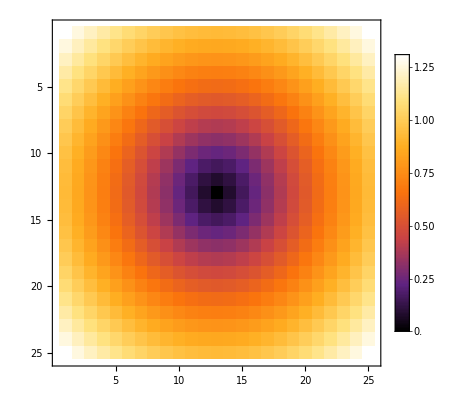

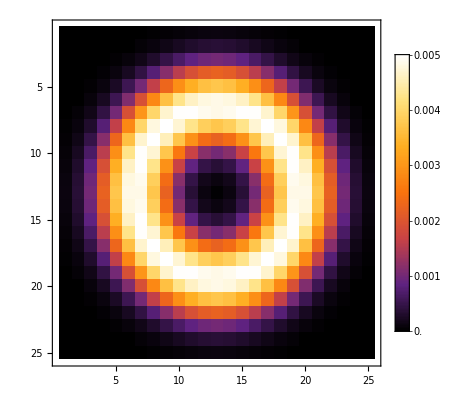

```mathematica
gaussienne[x_,mu_,sigma_]:=Exp[-0.5((x-mu)^2)/( sigma^2)];

distance=Table[EuclideanDistance[{i,j},{13,13}],{i,1,25},{j,1,25}]/13;
kernel=Map[gaussienne[#,μ,σ]&,distance,{2}];
kernel=ReplacePart[kernel,Position[distance,d_/;d>1]->0];
sum=Total[Flatten[kernel]];
kernel=kernel/sum;


ArrayPlot[distance,ColorFunction->"SunsetColors",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLegends->Automatic]
ArrayPlot[kernel,ColorFunction->"SunsetColors",Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLegends->Automatic]
```

## Fonction de croissance

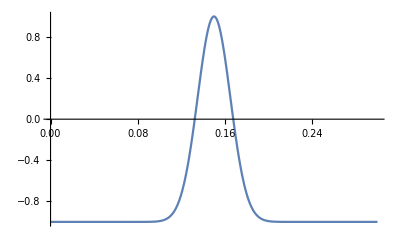

```mathematica
growthLenia[u_]:=-1+2*gaussienne[u,0.15,0.015]

Plot[growthLenia[x],{x,0,0.3},PlotRange->Full]
```

## Fonction d’évolution

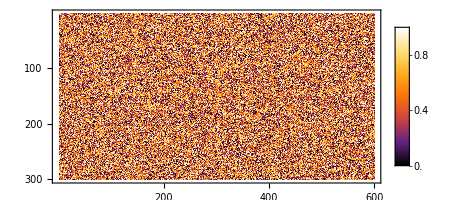

```mathematica
grid = RandomReal[{0, 1}, {300, 600}];
ArrayPlot[grid, ColorFunction -> "SunsetColors", Frame -> True, FrameTicks -> {{Automatic, None}, {Automatic, None}}, PlotLegends -> Automatic]


evolveLenia[X_] := Module[{U, newX},
  U = ListConvolve[kernel, X, {13, 13}, 0, Modulus -> 1];
  newX = X + dt*growthLenia[U];
  newX = Clip[newX, {0, 1}];
  Return[newX]]
```

## Etat initial - Random

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

$Aborted

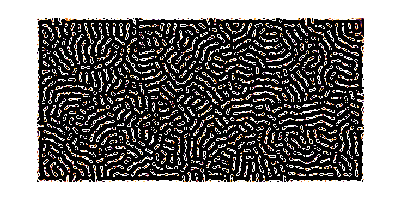

```mathematica
anim = Animate[grid = evolveLenia[grid];
   ArrayPlot[grid, ColorFunction -> "SunsetColors", ImageSize -> Large], {t, 0, 50,dt},AnimationRate->10];
Export["/Users/diegolallemand/phys/chaos/lenia/random_r13.mp4", anim,"AnimationDuration"->50]
ArrayPlot[grid, ColorFunction -> "SunsetColors"]
```

## Etat initial - Gaussienne

```mathematica
rows=512;
cols=512;

radius=72;
maxValue=1;

evolveGauss[X_] := Module[{U, newX},
  U = ListConvolve[kernel, X, {13, 13}, 0, Modulus -> 1];
  newX = X + dt*growthLenia[U];
  newX = Clip[newX, {0, 1}];
  Return[newX]]


centerX=(cols+1)/2;
centerY=(rows+1)/2;

gauss=Table[distance=Sqrt[(i-centerX)^2+(j-centerY)^2];
value=Exp[-(distance^2/(2*radius^2))];
normalizedValue=value/maxValue,{i,1,rows},{j,1,cols}];

ArrayPlot[gauss,ColorFunction->"SunsetColors",Mesh->None,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotLegends->Automatic]
```

1

-Graphics-

```mathematica
anim=Animate[gauss=evolveGauss[gauss];
ArrayPlot[gauss,ColorFunction->"SunsetColors",ImageSize->Large],{t,0,40,dt},AnimationRate->40/4 ];
Export["/Users/diegolallemand/phys/chaos/lenia/gauss_r20.mp4", anim,"AnimationDuration"->40]
ArrayPlot[gauss, ColorFunction -> "SunsetColors"]
```

/Users/diegolallemand/phys/chaos/lenia/gauss_r20.mp4

-Graphics-

## Orbium

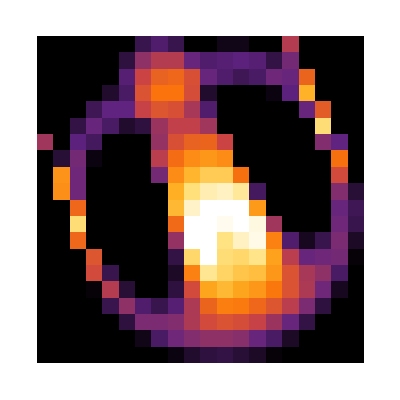

```mathematica
orbium={{0,0,0,0,0,0,0.1,0.14,0.1,0,0,0.03,0.03,0,0,0.3,0,0,0,0},{0,0,0,0,0,0.08,0.24,0.3,0.3,0.18,0.14,0.15,0.16,0.15,0.09,0.2,0,0,0,0},{0,0,0,0,0,0.15,0.34,0.44,0.46,0.38,0.18,0.14,0.11,0.13,0.19,0.18,0.45,0,0,0},{0,0,0,0,0.06,0.13,0.39,0.5,0.5,0.37,0.06,0,0,0,0.02,0.16,0.68,0,0,0},{0,0,0,0.11,0.17,0.17,0.33,0.4,0.38,0.28,0.14,0,0,0,0,0,0.18,0.42,0,0},{0,0,0.09,0.18,0.13,0.06,0.08,0.26,0.32,0.32,0.27,0,0,0,0,0,0,0.82,0,0},{0.27,0,0.16,0.12,0,0,0,0.25,0.38,0.44,0.45,0.34,0,0,0,0,0,0.22,0.17,0},{0,0.07,0.2,0.02,0,0,0,0.31,0.48,0.57,0.6,0.57,0,0,0,0,0,0,0.49,0},{0,0.59,0.19,0,0,0,0,0.2,0.57,0.69,0.76,0.76,0.49,0,0,0,0,0,0.36,0},{0,0.58,0.19,0,0,0,0,0,0.67,0.83,0.9,0.92,0.87,0.12,0,0,0,0,0.22,0.07},{0,0,0.46,0,0,0,0,0,0.7,0.93,1,1,1,0.61,0,0,0,0,0.18,0.11},{0,0,0.82,0,0,0,0,0,0.47,1,1,0.98,1,0.96,0.27,0,0,0,0.19,0.1},{0,0,0.46,0,0,0,0,0,0.25,1,1,0.84,0.92,0.97,0.54,0.14,0.04,0.1,0.21,0.05},{0,0,0,0.4,0,0,0,0,0.09,0.8,1,0.82,0.8,0.85,0.63,0.31,0.18,0.19,0.2,0.01},{0,0,0,0.36,0.1,0,0,0,0.05,0.54,0.86,0.79,0.74,0.72,0.6,0.39,0.28,0.24,0.13,0},{0,0,0,0.01,0.3,0.07,0,0,0.08,0.36,0.64,0.7,0.64,0.6,0.51,0.39,0.29,0.19,0.04,0},{0,0,0,0,0.1,0.24,0.14,0.1,0.15,0.29,0.45,0.53,0.52,0.46,0.4,0.31,0.21,0.08,0,0},{0,0,0,0,0,0.08,0.21,0.21,0.22,0.29,0.36,0.39,0.37,0.33,0.26,0.18,0.09,0,0,0},{0,0,0,0,0,0,0.03,0.13,0.19,0.22,0.24,0.24,0.23,0.18,0.13,0.05,0,0,0,0},{0,0,0,0,0,0,0,0,0.02,0.06,0.08,0.09,0.07,0.05,0.01,0,0,0,0,0}};

ArrayPlot[orbium,ColorFunction->"SunsetColors"]
orbiuminit=ArrayPad[orbium,{{40,128-Length[orbium]},{40,200-Length[orbium[[1]]]}},0];
anim = Animate[orbiuminit = evolveLenia[orbiuminit];
   ArrayPlot[orbiuminit, ColorFunction -> "SunsetColors", ImageSize -> Large], {t, 0, 10,dt},AnimationRate->10]
```